# Monopoly Startup Growth Model

## Context

Companies show different growth rates according to its stages.

At its first stages, startups amass roughly no market share in absolute values, however show relatively high growth rates.

At its last stages, startups show virtually no market share gain provided no competitors play in the market. That is because they approach SOM (the total obtainable market size in its sector).

In the middle of the game, they show relatively high growth rates matching high market share gain. At this point, growth rates and market share gain are in perfect equilibrium. This is the point where VCs go onto last rounds to IPOs.

## Theory and simulation

A[x] is the logistic shifted function. Shift is a parameter controlling where its mean growth life stands.

```mathematica
shift=-5;
A[x_]=1/(1+Exp[-(x+shift)])
```

1/(1+ⅇ^(5-x))

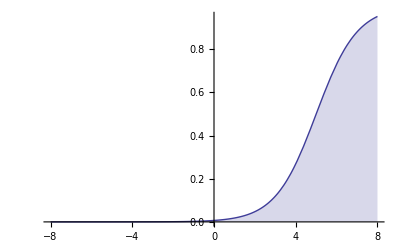

```mathematica
Plot[A[x],{x,-8,8},Filling->Bottom,AxesOrigin->{0,0}]
```

B[x] is A[x]’s first derivative. It stands for growth rates distributions around the shifting point.

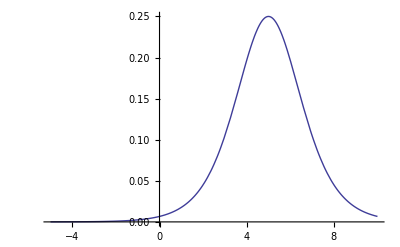

```mathematica
B[x_]:=ⅇ^(5-x)/((1+ⅇ^(5-x))^2)
Plot[B[x],{x,-5,10}]
```